```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.7,cj->U/5,U->5,t23->x t22,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→5,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

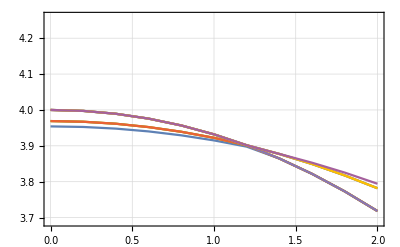

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

5.13561×10^-6

1

0.0001328

1

0.00051614

1

0.00115619

1

0.00205463

1

0.00321379

1

0.00463653

1

0.00632621

1

0.00828655

1

0.0105216

1

0.0130354

1

0.0158322

1

0.0189157

1

5.88235

1

5.86032

1

5.83604

1

5.80955

1

5.78089

1

5.75017

1

5.71752

1

5.68311

2

2.

2

1.99988

2

1.99952

2

1.99893

2

1.9981

2

1.99703

2

1.99572

2

1.99416

2

1.99236

2

1.99031

2

1.98802

2

1.98546

2

5.90216

2

5.88235

2

5.86032

2

5.83604

2

5.80955

2

5.78089

2

5.75017

2

5.71752

2

5.68311

3

2.

3

1.99988

3

1.99952

3

1.99893

3

1.9981

3

1.99703

3

1.99572

3

1.99416

3

1.99236

3

1.99031

3

1.98802

3

1.98546

3

5.90216

3

5.88235

3

5.86032

3

5.83604

3

5.80955

3

5.78089

3

5.75017

3

5.71752

3

5.68311

4

2.

4

1.99988

4

1.99952

4

1.99893

4

1.9981

4

1.99703

4

1.99572

4

1.99416

4

1.99236

4

1.99031

4

1.98802

4

1.98546

4

5.90216

4

5.88235

4

5.86032

4

5.83604

4

5.80955

4

5.78089

4

5.75017

4

5.71752

4

5.68311

5

6.

5

5.99944

5

5.99776

5

5.99492

5

5.99085

5

5.98549

5

5.97872

5

5.97045

5

5.96055

5

5.94888

5

5.93534

5

5.9198

5

5.90216

5

5.88235

5

5.86032

5

5.83604

5

5.80955

5

5.78089

5

5.75017

5

5.71752

5

5.68311

6

6.

6

5.99944

6

5.99776

6

5.99492

6

5.99085

6

5.98549

6

5.97872

6

5.97045

6

5.96055

6

5.94888

6

5.93534

6

5.9198

6

5.90216

6

0.0222897

6

0.0259569

6

1.97266

6

1.9688

6

1.96467

6

1.96026

6

1.95558

6

1.95062

7

6.

7

5.99944

7

5.99776

7

5.99492

7

5.99085

7

5.98549

7

5.97872

7

5.97045

7

5.96055

7

5.94888

7

5.93534

7

5.9198

7

1.98266

7

1.97959

7

1.97626

7

1.97266

7

1.9688

7

1.96467

7

1.96026

7

1.95558

7

1.95062

8

6.

8

5.99944

8

5.99776

8

5.99492

8

5.99085

8

5.98549

8

5.97872

8

5.97045

8

5.96055

8

5.94888

8

5.93534

8

5.9198

8

1.98266

8

1.97959

8

1.97626

8

1.97266

8

1.9688

8

1.96467

8

1.96026

8

1.95558

8

1.95062

9

6.

9

5.99944

9

5.99776

9

5.99492

9

5.99085

9

5.98549

9

5.97872

9

5.97045

9

5.96055

9

5.94888

9

5.93534

9

5.9198

9

1.98266

9

1.97959

9

1.97626

9

0.0299194

9

0.0341782

9

0.0387331

9

0.0435821

9

0.0487216

9

0.0541461

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.741389

10

0.74018

10

0.738927

10

0.737637

10

0.736317

10

0.734975

10

0.733618

10

0.732253

```mathematica
data1//MatrixForm
```

(1 | 0. | 5.13561×10^-6 | 3.95412
1 | 0.1 | 0.0001328 | 3.95374
1 | 0.2 | 0.00051614 | 3.95258
1 | 0.3 | 0.00115619 | 3.95064
1 | 0.4 | 0.00205463 | 3.94793
1 | 0.5 | 0.00321379 | 3.94443
1 | 0.6 | 0.00463653 | 3.94015
1 | 0.7 | 0.00632621 | 3.93508
1 | 0.8 | 0.00828655 | 3.92922
1 | 0.9 | 0.0105216 | 3.92255
1 | 1. | 0.0130354 | 3.91508
1 | 1.1 | 0.0158322 | 3.9068
1 | 1.2 | 0.0189157 | 3.89769
1 | 1.3 | 5.88235 | 3.8837
1 | 1.4 | 5.86032 | 3.8646
1 | 1.5 | 5.83604 | 3.84398
1 | 1.6 | 5.80955 | 3.82182
1 | 1.7 | 5.78089 | 3.79815
1 | 1.8 | 5.75017 | 3.77295
1 | 1.9 | 5.71752 | 3.74625
1 | 2. | 5.68311 | 3.71807
2 | 0. | 2. | 3.96899
2 | 0.1 | 1.99988 | 3.96852
2 | 0.2 | 1.99952 | 3.96713
2 | 0.3 | 1.99893 | 3.9648
2 | 0.4 | 1.9981 | 3.96153
2 | 0.5 | 1.99703 | 3.95734
2 | 0.6 | 1.99572 | 3.9522
2 | 0.7 | 1.99416 | 3.94614
2 | 0.8 | 1.99236 | 3.93913
2 | 0.9 | 1.99031 | 3.93119
2 | 1. | 1.98802 | 3.92231
2 | 1.1 | 1.98546 | 3.9125
2 | 1.2 | 5.90216 | 3.90129
2 | 1.3 | 5.88235 | 3.8837
2 | 1.4 | 5.86032 | 3.8646
2 | 1.5 | 5.83604 | 3.84398
2 | 1.6 | 5.80955 | 3.82182
2 | 1.7 | 5.78089 | 3.79815
2 | 1.8 | 5.75017 | 3.77295
2 | 1.9 | 5.71752 | 3.74625
2 | 2. | 5.68311 | 3.71807
3 | 0. | 2. | 3.96899
3 | 0.1 | 1.99988 | 3.96852
3 | 0.2 | 1.99952 | 3.96713
3 | 0.3 | 1.99893 | 3.9648
3 | 0.4 | 1.9981 | 3.96153
3 | 0.5 | 1.99703 | 3.95734
3 | 0.6 | 1.99572 | 3.9522
3 | 0.7 | 1.99416 | 3.94614
3 | 0.8 | 1.99236 | 3.93913
3 | 0.9 | 1.99031 | 3.93119
3 | 1. | 1.98802 | 3.92231
3 | 1.1 | 1.98546 | 3.9125
3 | 1.2 | 5.90216 | 3.90129
3 | 1.3 | 5.88235 | 3.8837
3 | 1.4 | 5.86032 | 3.8646
3 | 1.5 | 5.83604 | 3.84398
3 | 1.6 | 5.80955 | 3.82182
3 | 1.7 | 5.78089 | 3.79815
3 | 1.8 | 5.75017 | 3.77295
3 | 1.9 | 5.71752 | 3.74625
3 | 2. | 5.68311 | 3.71807
4 | 0. | 2. | 3.96899
4 | 0.1 | 1.99988 | 3.96852
4 | 0.2 | 1.99952 | 3.96713
4 | 0.3 | 1.99893 | 3.9648
4 | 0.4 | 1.9981 | 3.96153
4 | 0.5 | 1.99703 | 3.95734
4 | 0.6 | 1.99572 | 3.9522
4 | 0.7 | 1.99416 | 3.94614
4 | 0.8 | 1.99236 | 3.93913
4 | 0.9 | 1.99031 | 3.93119
4 | 1. | 1.98802 | 3.92231
4 | 1.1 | 1.98546 | 3.9125
4 | 1.2 | 5.90216 | 3.90129
4 | 1.3 | 5.88235 | 3.8837
4 | 1.4 | 5.86032 | 3.8646
4 | 1.5 | 5.83604 | 3.84398
4 | 1.6 | 5.80955 | 3.82182
4 | 1.7 | 5.78089 | 3.79815
4 | 1.8 | 5.75017 | 3.77295
4 | 1.9 | 5.71752 | 3.74625
4 | 2. | 5.68311 | 3.71807
5 | 0. | 6. | 4.
5 | 0.1 | 5.99944 | 3.99933
5 | 0.2 | 5.99776 | 3.99733
5 | 0.3 | 5.99492 | 3.99399
5 | 0.4 | 5.99085 | 3.98929
5 | 0.5 | 5.98549 | 3.98324
5 | 0.6 | 5.97872 | 3.97581
5 | 0.7 | 5.97045 | 3.96698
5 | 0.8 | 5.96055 | 3.95675
5 | 0.9 | 5.94888 | 3.94508
5 | 1. | 5.93534 | 3.93196
5 | 1.1 | 5.9198 | 3.91737
5 | 1.2 | 5.90216 | 3.90129
5 | 1.3 | 5.88235 | 3.8837
5 | 1.4 | 5.86032 | 3.8646
5 | 1.5 | 5.83604 | 3.84398
5 | 1.6 | 5.80955 | 3.82182
5 | 1.7 | 5.78089 | 3.79815
5 | 1.8 | 5.75017 | 3.77295
5 | 1.9 | 5.71752 | 3.74625
5 | 2. | 5.68311 | 3.71807
6 | 0. | 6. | 4.
6 | 0.1 | 5.99944 | 3.99933
6 | 0.2 | 5.99776 | 3.99733
6 | 0.3 | 5.99492 | 3.99399
6 | 0.4 | 5.99085 | 3.98929
6 | 0.5 | 5.98549 | 3.98324
6 | 0.6 | 5.97872 | 3.97581
6 | 0.7 | 5.97045 | 3.96698
6 | 0.8 | 5.96055 | 3.95675
6 | 0.9 | 5.94888 | 3.94508
6 | 1. | 5.93534 | 3.93196
6 | 1.1 | 5.9198 | 3.91737
6 | 1.2 | 5.90216 | 3.90129
6 | 1.3 | 0.0222897 | 3.88776
6 | 1.4 | 0.0259569 | 3.87698
6 | 1.5 | 1.97266 | 3.86381
6 | 1.6 | 1.9688 | 3.84928
6 | 1.7 | 1.96467 | 3.83381
6 | 1.8 | 1.96026 | 3.8174
6 | 1.9 | 1.95558 | 3.80005
6 | 2. | 1.95062 | 3.78177
7 | 0. | 6. | 4.
7 | 0.1 | 5.99944 | 3.99933
7 | 0.2 | 5.99776 | 3.99733
7 | 0.3 | 5.99492 | 3.99399
7 | 0.4 | 5.99085 | 3.98929
7 | 0.5 | 5.98549 | 3.98324
7 | 0.6 | 5.97872 | 3.97581
7 | 0.7 | 5.97045 | 3.96698
7 | 0.8 | 5.96055 | 3.95675
7 | 0.9 | 5.94888 | 3.94508
7 | 1. | 5.93534 | 3.93196
7 | 1.1 | 5.9198 | 3.91737
7 | 1.2 | 1.98266 | 3.90174
7 | 1.3 | 1.97959 | 3.89004
7 | 1.4 | 1.97626 | 3.87739
7 | 1.5 | 1.97266 | 3.86381
7 | 1.6 | 1.9688 | 3.84928
7 | 1.7 | 1.96467 | 3.83381
7 | 1.8 | 1.96026 | 3.8174
7 | 1.9 | 1.95558 | 3.80005
7 | 2. | 1.95062 | 3.78177
8 | 0. | 6. | 4.
8 | 0.1 | 5.99944 | 3.99933
8 | 0.2 | 5.99776 | 3.99733
8 | 0.3 | 5.99492 | 3.99399
8 | 0.4 | 5.99085 | 3.98929
8 | 0.5 | 5.98549 | 3.98324
8 | 0.6 | 5.97872 | 3.97581
8 | 0.7 | 5.97045 | 3.96698
8 | 0.8 | 5.96055 | 3.95675
8 | 0.9 | 5.94888 | 3.94508
8 | 1. | 5.93534 | 3.93196
8 | 1.1 | 5.9198 | 3.91737
8 | 1.2 | 1.98266 | 3.90174
8 | 1.3 | 1.97959 | 3.89004
8 | 1.4 | 1.97626 | 3.87739
8 | 1.5 | 1.97266 | 3.86381
8 | 1.6 | 1.9688 | 3.84928
8 | 1.7 | 1.96467 | 3.83381
8 | 1.8 | 1.96026 | 3.8174
8 | 1.9 | 1.95558 | 3.80005
8 | 2. | 1.95062 | 3.78177
9 | 0. | 6. | 4.
9 | 0.1 | 5.99944 | 3.99933
9 | 0.2 | 5.99776 | 3.99733
9 | 0.3 | 5.99492 | 3.99399
9 | 0.4 | 5.99085 | 3.98929
9 | 0.5 | 5.98549 | 3.98324
9 | 0.6 | 5.97872 | 3.97581
9 | 0.7 | 5.97045 | 3.96698
9 | 0.8 | 5.96055 | 3.95675
9 | 0.9 | 5.94888 | 3.94508
9 | 1. | 5.93534 | 3.93196
9 | 1.1 | 5.9198 | 3.91737
9 | 1.2 | 1.98266 | 3.90174
9 | 1.3 | 1.97959 | 3.89004
9 | 1.4 | 1.97626 | 3.87739
9 | 1.5 | 0.0299194 | 3.86536
9 | 1.6 | 0.0341782 | 3.85289
9 | 1.7 | 0.0387331 | 3.83955
9 | 1.8 | 0.0435821 | 3.82533
9 | 1.9 | 0.0487216 | 3.81024
9 | 2. | 0.0541461 | 3.79427
10 | 0. | 3.75 | 4.53381
10 | 0.1 | 3.75 | 4.53381
10 | 0.2 | 3.75 | 4.53381
10 | 0.3 | 3.75 | 4.53381
10 | 0.4 | 3.75 | 4.53381
10 | 0.5 | 3.75 | 4.53381
10 | 0.6 | 3.75 | 4.53381
10 | 0.7 | 3.75 | 4.53381
10 | 0.8 | 3.75 | 4.53381
10 | 0.9 | 3.75 | 4.53381
10 | 1. | 3.75 | 4.53381
10 | 1.1 | 3.75 | 4.53381
10 | 1.2 | 3.75 | 4.53381
10 | 1.3 | 0.741389 | 4.52285
10 | 1.4 | 0.74018 | 4.50497
10 | 1.5 | 0.738927 | 4.48581
10 | 1.6 | 0.737637 | 4.4654
10 | 1.7 | 0.736317 | 4.44373
10 | 1.8 | 0.734975 | 4.42082
10 | 1.9 | 0.733618 | 4.39669
10 | 2. | 0.732253 | 4.37135)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;13,1;;4]];
tmp02 = data1[[119;;120,1;;4]];
tmp03 = data1[[184;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;33,1;;4]];
tmp02 = data1[[139;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.95412 | 5.13561×10^-6
0.1 | 3.95374 | 0.0001328
0.2 | 3.95258 | 0.00051614
0.3 | 3.95064 | 0.00115619
0.4 | 3.94793 | 0.00205463
0.5 | 3.94443 | 0.00321379
0.6 | 3.94015 | 0.00463653
0.7 | 3.93508 | 0.00632621
0.8 | 3.92922 | 0.00828655
0.9 | 3.92255 | 0.0105216
1. | 3.91508 | 0.0130354
1.1 | 3.9068 | 0.0158322
1.2 | 3.89769 | 0.0189157
1.3 | 3.88776 | 0.0222897
1.4 | 3.87698 | 0.0259569
1.5 | 3.86536 | 0.0299194
1.6 | 3.85289 | 0.0341782
1.7 | 3.83955 | 0.0387331
1.8 | 3.82533 | 0.0435821
1.9 | 3.81024 | 0.0487216
2. | 3.79427 | 0.0541461)

(0. | 3.96899 | 2.
0.1 | 3.96852 | 1.99988
0.2 | 3.96713 | 1.99952
0.3 | 3.9648 | 1.99893
0.4 | 3.96153 | 1.9981
0.5 | 3.95734 | 1.99703
0.6 | 3.9522 | 1.99572
0.7 | 3.94614 | 1.99416
0.8 | 3.93913 | 1.99236
0.9 | 3.93119 | 1.99031
1. | 3.92231 | 1.98802
1.1 | 3.9125 | 1.98546
1.2 | 3.90174 | 1.98266
1.3 | 3.89004 | 1.97959
1.4 | 3.87739 | 1.97626
1.5 | 3.86381 | 1.97266
1.6 | 3.84928 | 1.9688
1.7 | 3.83381 | 1.96467
1.8 | 3.8174 | 1.96026
1.9 | 3.80005 | 1.95558
2. | 3.78177 | 1.95062)

(0. | 4. | 6.
0.1 | 3.99933 | 5.99944
0.2 | 3.99733 | 5.99776
0.3 | 3.99399 | 5.99492
0.4 | 3.98929 | 5.99085
0.5 | 3.98324 | 5.98549
0.6 | 3.97581 | 5.97872
0.7 | 3.96698 | 5.97045
0.8 | 3.95675 | 5.96055
0.9 | 3.94508 | 5.94888
1. | 3.93196 | 5.93534
1.1 | 3.91737 | 5.9198
1.2 | 3.90129 | 5.90216
1.3 | 3.8837 | 5.88235
1.4 | 3.8646 | 5.86032
1.5 | 3.84398 | 5.83604
1.6 | 3.82182 | 5.80955
1.7 | 3.79815 | 5.78089
1.8 | 3.77295 | 5.75017
1.9 | 3.74625 | 5.71752
2. | 3.71807 | 5.68311)

```mathematica
|
```

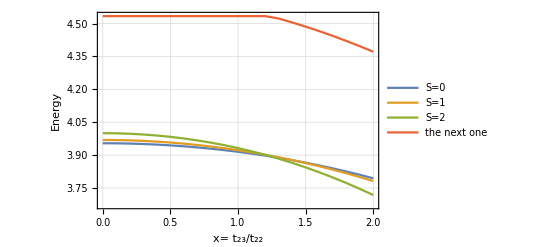

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

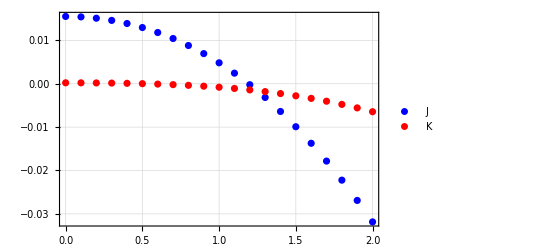

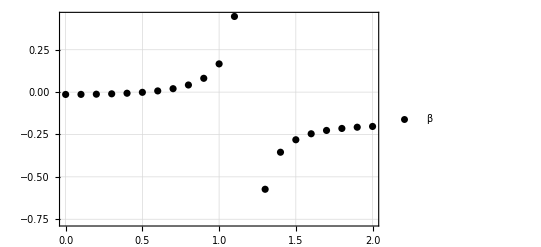

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```